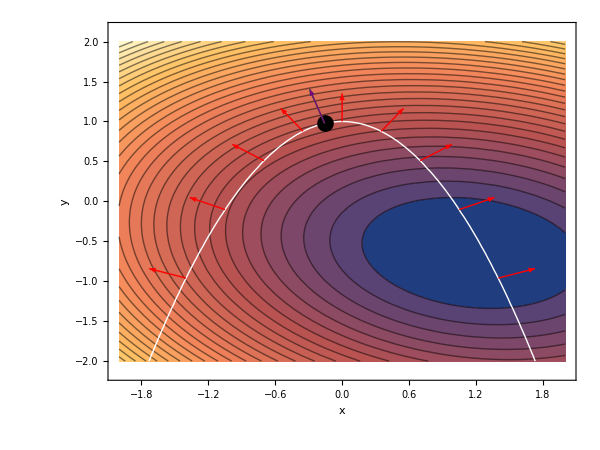

```mathematica
(*----------Define loss and constraint----------*)(*1) 定义目标与约束*)ClearAll[f,g,x,y];
f[x_,y_]:=(x-1)^2+2 (y+1/2)^2+0.5 x y;
g[x_,y_]:=x^2+y-1;

(*2) 先“符号”梯度，再“数值”代入*)
gradf[x_,y_]:={D[f[x,y],x],D[f[x,y],y]};
gradg[x_,y_]:={D[g[x,y],x],D[g[x,y],y]};

(*一个小助手：在点 {x0,y0} 评价向量场*)
at[vec_,{x0_,y0_}]:=(vec/. {x->x0,y->y0})//N;

(*例子：在 {-1.4,0.3} 处求梯度（不会触发 D::ivar）*)
gf=at[gradf[x,y],{-1.4,0.3}];  (* ->{…,…} 长度应为 2*)
gg=at[gradg[x,y],{-1.4,0.3}];

(*取分量一定用[[]]，而且变量名别打成 ngl/nl g 这类错别字*)
n1=gg[[1]];
n2=gg[[2]];
tangent={-n2,n1};  (*与 ∇g 正交的切向*)
(*----------Constrained minimizer:∇f=λ ∇g with g=0----------*)
sol=NSolve[{D[f[x,y],x]==λ D[g[x,y],x],D[f[x,y],y]==λ D[g[x,y],y],g[x,y]==0},{x,y,λ},Reals];

pstar={x,y}/. First[sol]//N;   (*取一个实解作为约束极小点*)
(*可查看：pstar*)

(*----------Sampling points on the constraint curve g=0----------*)
(*采样曲线点*)curve[x0_]:={x0,1-x0^2};
samples=Table[curve[x0],{x0,-1.4,1.4,0.35}];

arrowScale=0.35;

normalsGraphics=Graphics[{Thick,Red,Table[With[{p=pt,ng=at[gradg[x,y],pt]},Arrow[{p,p+arrowScale Normalize[ng]}]],{pt,samples}]}];

tangentsGraphics=Graphics[{Thick,Blue,Opacity[0.45],Table[With[{p=pt,ng=at[gradg[x,y],pt],t={-at[gradg[x,y],pt][[2]],at[gradg[x,y],pt][[1]]}},Arrow[{p,p+arrowScale Normalize[t]}]],{pt,samples}]}];

(*约束极小点：解 ∇f=λ ∇g,g=0*)
Clear[λ];
sol=NSolve[{D[f[x,y],x]==λ D[g[x,y],x],D[f[x,y],y]==λ D[g[x,y],y],g[x,y]==0},{x,y,λ},Reals];

pstar={x,y}/. First[sol]//N;

starArrows=Module[{gf=at[gradf[x,y],pstar],gg=at[gradg[x,y],pstar]},Graphics[{Black,PointSize[0.02],Point[pstar],Text[Style["",14],pstar+{0.08,0.08}],Thick,Darker@Green,Arrow[{pstar,pstar+0.45 Normalize[gf]}],Purple,Arrow[{pstar,pstar+0.45 Normalize[gg]}]}]];
(*----------Base plots:loss contours+constraint curve----------*)
cp=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},Contours->30,ContourShading->Automatic,Frame->True,FrameLabel->(Style[#,13]&/@{"x","y"}),AspectRatio->3/4,(*4:3 画幅*)ImageSize->600];

constraintCurve=ContourPlot[g[x,y]==0,{x,-2,2},{y,-2,2},ContourStyle->{White,Thick},Contours->{0},ContourShading->False];

(*可选：叠加 ∇f 的稀疏向量场，帮助理解下降方向*)
vf=VectorPlot[Evaluate[gradf[x,y]],{x,-2,2},{y,-2,2},VectorPoints->15,VectorStyle->Directive[GrayLevel[0],Opacity[0]],VectorScale->Small];

Show[cp,vf,constraintCurve,normalsGraphics,starArrows,PlotRange->All]
```

```mathematica
Rasterize[%218,"Image"]
```

-Graphics-

```mathematica
Rasterize[%156,"Image"]
```

-Graphics-